FittedModel[0.357082 (-4.46617+x)]

| Estimate | Standard Error | t-Statistic | P-Value
a | 4.46617 | 3.35456 | 1.33137 | 0.410115
b | 0.357082 | 0.00465026 | 76.7876 | 0.00829019

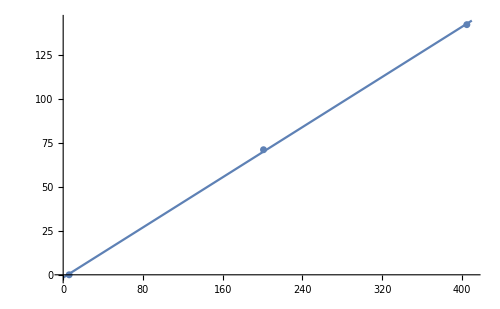

```mathematica
energy = {0, 142.5/2, 142.5};
channels = {6, 201, 405};
data = Transpose[{channels, energy}];
nlm = NonlinearModelFit[data, b( x-a), {a, b}, x]
nlm["ParameterTable"]
Show[Plot[Normal[nlm], {x, 0, 410}, ImageSize->500],ListPlot[data, PlotStyle->{PointSize[0.01]}]]
```

```mathematica
Solve[Normal[nlm] == 52, x]
```

{{x→150.091}}

```mathematica
-20 Log[10,150/405] //N
```

8.62728

```mathematica
-20 Log[10,150/201] //N
```

2.5421